# Practical 2(b) Anurag kumar | 20211405 | B.Sc Computer Science(Hons) | Semester 4

## Regula Falsi Method

## Question 1

x0=1

x1=2

Nmax=10

epsilone 1/10000

f(x):=Cos[x]

1th iterations value is:1.564904375891578

Estimated error is:1.

2th iterations value is:1.57097857453502

Estimated error is:0.435095624108422

3th iterations value is:1.57079632577305

Estimated error is:0.00607419864344

Return[1.5707963267949]

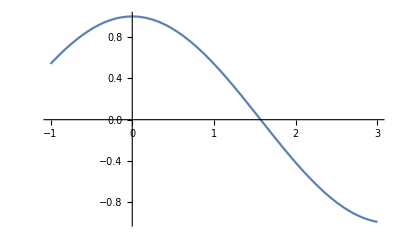

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of coveregence parameter"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilone",eps];
f[x_]=Cos[x];
Print["f(x):=",f[x]]; If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the value."],
For[i=1,i≤Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],
Print[i,"th iterations value is:",N[a,16]]
Print["Estimated error is:",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is:",N[a,16]]
Print["Estimated error is:",N[x1-x0,16]]]
Plot[f[x],{x,-1,3}]
```

## Question2

x0=1

x1=2

Nmax=10

epsilone 1/10000

f(x):=1-5 x+x^3

These values do not satisfy the IVP so change the value.

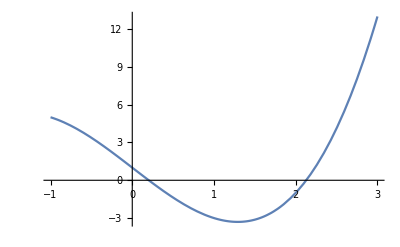

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of coveregence parameter"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilone",eps];
f[x_]=x^3-5*x+1;
Print["f(x):=",f[x]]; If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the value."],
For[i=1,i≤Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],
Print[i,"th iterations value is:",N[a,16]]
Print["Estimated error is:",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is:",N[a,16]]
Print["Estimated error is:",N[x1-x0,16]]]
Plot[f[x],{x,-1,3}]
```

## Question3

x0=1

x1=2

Nmax=10

epsilone 1/10000

f(x):=-ⅇ^x x+Cos[x]

These values do not satisfy the IVP so change the value.

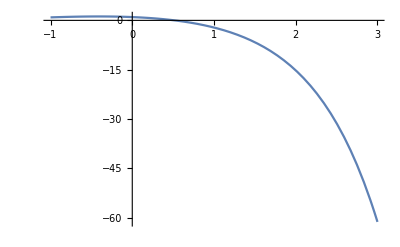

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of coveregence parameter"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilone",eps];
f[x_]=Cos[x]-x*Exp[x];
Print["f(x):=",f[x]]; If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the value."],
For[i=1,i≤Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],
Print[i,"th iterations value is:",N[a,16]]
Print["Estimated error is:",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is:",N[a,16]]
Print["Estimated error is:",N[x1-x0,16]]]
Plot[f[x],{x,-1,3}]
```